# Using the SACNA package - Calvin LES model

The purpose of this document is to give a short tutorial for the SACNA package. 
Let’s start by bringing the package functions to this notebook.

```mathematica
Quiet[ClearAll["Global`*"]];
 Quiet[Remove["Global`*"]];
SetDirectory[NotebookDirectory[]];

Quiet[Get["../SACNA.wl"]]
```

Now let’s input the reactions and rates lists of this model. If we input the rates list as an empty list, SACNA will assign rates by default. Reactions must be in terms of D-species, L-species, Z-species (achiral species), and the empty specie N1.

```mathematica
(*Calvin-LES model*)
reactions = {"L1->D1","D1->L1","L1->L2","L2->L1","D1->D2","D2->D1","L1+L2->2L2","2L2->L1+L2","D1+D2->2D2","2D2->D1+D2","L1+L2->L2+D2","L2+D2->L1+L2","D1+D2->D2+L2","D2+L2->D1+D2"};
rates={};
```

Now we can run the semialgebraic analysis of the model by using the RunSemiAlgebraicAnalysis function. The first parameter corresponds to the reactions’ list, the second parameter corresponds to the rates’ list, and the last parameter corresponds to time in seconds (the Collins’ algorithm may take so much time to find a solution). The function will ask for the Routh-Hurwitz condition number. Considering the first and last numbers will be faster, because this conditions are shorter than the others.  For this particular example we will be choose the first condition.

```mathematica
time=60;
cadSolutions=RunSemiAlgebraicAnalysis[reactions,rates,time]
```

D1>0&&0<D2<D1&&k1>0&&k2>0&&k3>0&&k4>(2 k1+k2+k3)/(D1-D2)&&0<k5<(-2 k1-k2-k3+D1 k4-D2 k4)/(2 D2)&&0<k6<(-2 k1-k2-k3+D1 k4-D2 k4-2 D2 k5)/(D1+D2)&&k7==(D1 k2-D2 k3+D1 D2 k4-D2^2 k5+D1 D2 k6)/D2^2

As the algorithm found a solution, let’s find some particular solutions by using the FindInstance command.  Note that the solution doesn’t contain an expression for the L-species. It’s because we are assuming the racemic condition.

```mathematica
numberOfSamples=10; (*feel free to change*)
samplesList=FindInstance[cadSolutions,DeleteCases[DeleteDuplicates@Cases[cadSolutions,_Symbol,Infinity], Alternatives@@{GreaterEqual,Greater,Less,LessEqual}],numberOfSamples];
sampleNumber=8;   (*feel free to change*)
samplesList[[sampleNumber]]
```

{D1→769,D2→62,k1→24,k2→74,k3→63,k4→11,k5→29,k6→5/11,k7→1341048/10571}

Now we are ready to using the SACNA’s system simulator with the  ReactionSystemSimulator function

Species Concentrations Graphic

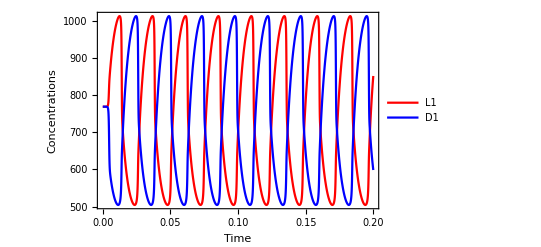

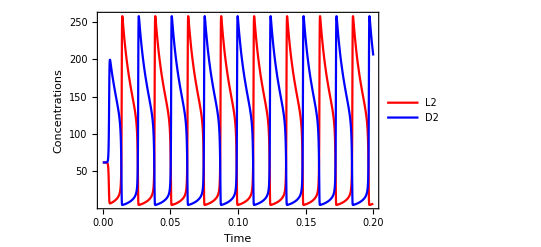

```mathematica
simulationTimeMin=0; 
simulationTimeMax=0.2; (*feel free to change*)
graficss=ReactionSystemSimulator[reactions,rates, samplesList[[sampleNumber]],0.00001,t,simulationTimeMin,simulationTimeMax];
```

SACNA also allows to export a simulation results to ChemKinLator simulator files with the function ExportToChemKinLator.

```mathematica
content=ExportToChemKinLator[reactions,rates, samplesList[[sampleNumber]],1/1000000000000000,1/1000000000000000,0,simulationTimeMax,1000];
```

Export::chtype: First argument $Canceled is not a valid file specification.

We can do the same analysis with the second Routh-Hurwitz condition.

D1>0&&D2>0&&k1>0&&k2>0&&k3>0&&k4>k3/D1&&0<k5<(-k3+D1 k4)/(2 D2)&&0<k6<(-k1 k3+D1 k1 k4-2 D2 k1 k5)/(D1 k1+D1 k2+D2 k3+2 D2^2 k5)&&k7==(D1 k2-D2 k3+D1 D2 k4-D2^2 k5+D1 D2 k6)/D2^2

{D1→769,D2→62,k1→24,k2→74,k3→63,k4→11,k5→29,k6→2/53,k7→12396201/101866}

Species Concentrations Graphic

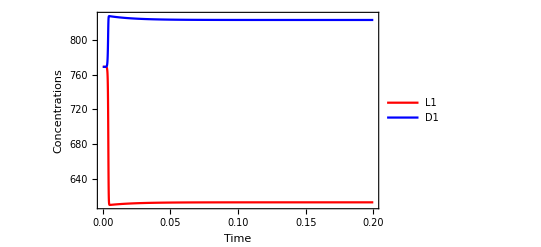

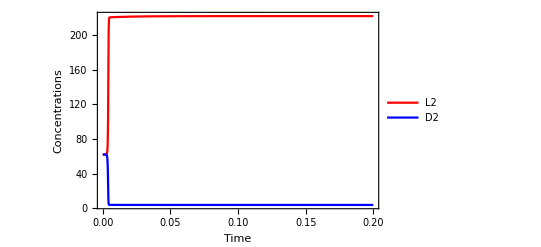

```mathematica
cadSolutions=RunSemiAlgebraicAnalysis[reactions,rates,time]
numberOfSamples=10; (*feel free to change*)
samplesList=FindInstance[cadSolutions,DeleteCases[DeleteDuplicates@Cases[cadSolutions,_Symbol,Infinity], Alternatives@@{GreaterEqual,Greater,Less,LessEqual}],numberOfSamples];
sampleNumber=8;   (*feel free to change*)
samplesList[[sampleNumber]]
simulationTimeMin=0; 
simulationTimeMax=0.2; (*feel free to change*)
graficss=ReactionSystemSimulator[reactions,rates, samplesList[[sampleNumber]],0.00001,t,simulationTimeMin,simulationTimeMax];
```